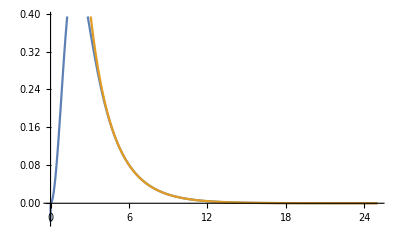

```mathematica
z1=1;
z2=1;
esq=1.4399764;
hBarSquared=41.801651165221026;
m1=1;
m2=2;
m=(m1 m2)/(m1+m2);
maxR=25.0;
minR=0.001;
Ε=-6.495;
W0=131.934;
R0=1.575;
Rcoul=1.575;
a0=0.65;

twoMuDevHBarSq=(2 m)/hBarSquared;
potentialWoodsSaxon[R_]:=-twoMuDevHBarSq W0/(1+Exp[(R-R0)/a0]);
L=1;
ksq=(2 m Ε)/hBarSquared ;
η=(esq z1 z2 m)/(hBarSquared √Abs[ksq]);
potentialCoulomb[R_]:=twoMuDevHBarSq If[R>Rcoul,
 esq(z1 z2)/R,
esq(z1 z2)/(2.Rcoul)(3.-R^2/Rcoul^2)];

Ρ={R,minR,maxR};
assymR=maxR;
assympWittakerDependedQ=True;
assympΧ=If[assympWittakerDependedQ,WhittakerW[-η,L+1/2,2 √Abs[ksq] assymR],0.0];
assympΧPrime=If[assympWittakerDependedQ,D[WhittakerW[-η,L+1/2,2 √Abs[ksq] x],x]/.x->assymR,0.1];
equationShrodinger={Χ''[R]+(ksq-1.0potentialWoodsSaxon[R]-1.0potentialCoulomb[R]-(L(L+1))/R^2)Χ[R]==0,
Χ[assymR]==assympΧ,Χ'[assymR]==assympΧPrime};
solution=NDSolve[equationShrodinger,Χ,Ρ];

Plot[{1.0Evaluate[Χ[R]/.solution],1.0WhittakerW[-η,L+1/2,2 √Abs[ksq] R]},Ρ]
```

```mathematica
assympΧ
```

0.0000105987+0. ⅈ